```mathematica
zb[t_,s_]:=E^((t+ArcTan[2s])I)Zeta[1/2-s I]+E^(-(t+ArcTan[2s])I)Zeta[1/2+s I]
zb1[s_]:=zb[0,s]
zb2[s_]:=zb[-Pi/2,s]
zt[s_]:=(zb1[s]+I zb2[s])/2
zt2[s_]:=-(zb1[s]-I zb2[s])/(2 I)
rat[s_]:=zb1[s]/zb2[s]
rata[s_]:=ⅈ-(2 ⅈ)/(1-(ⅇ^(2 ⅈ ArcTan[2 s]) Zeta[1/2-ⅈ s])/Zeta[1/2+ⅈ s])
zc[t_,s_]:=E^((t)I)Zeta[1/2-s I]+E^(-(t)I)Zeta[1/2+s I]
zc1[s_]:=zc[0,s]
zc2[s_]:=zc[-Pi/2,s]
ztc[s_]:=(zc1[s]+I zc2[s])/2
ztc2[s_]:=-(zc1[s]-I zc2[s])/(2 I)
```

```mathematica
FullSimplify[zb1[s]+I zb2[s]]
```

2 ⅇ^(ⅈ ArcTan[2 s]) Zeta[1/2-ⅈ s]

```mathematica
FullSimplify[zt[s]]
```

ⅇ^(ⅈ ArcTan[2 s]) Zeta[1/2-ⅈ s]

```mathematica
FullSimplify[zb1[s]/zb2[s]]
```

ⅈ-(2 ⅈ)/(1-(ⅇ^(2 ⅈ ArcTan[2 s]) Zeta[1/2-ⅈ s])/Zeta[1/2+ⅈ s])

```mathematica
FullSimplify[ⅈ-(2 ⅈ)/(1-ⅇ^(2 ⅈ ArcTan[2 s]))]
```

1/(2 s)

```mathematica
rat[N@Im@ZetaZero@3]
```

0.271911+0. ⅈ

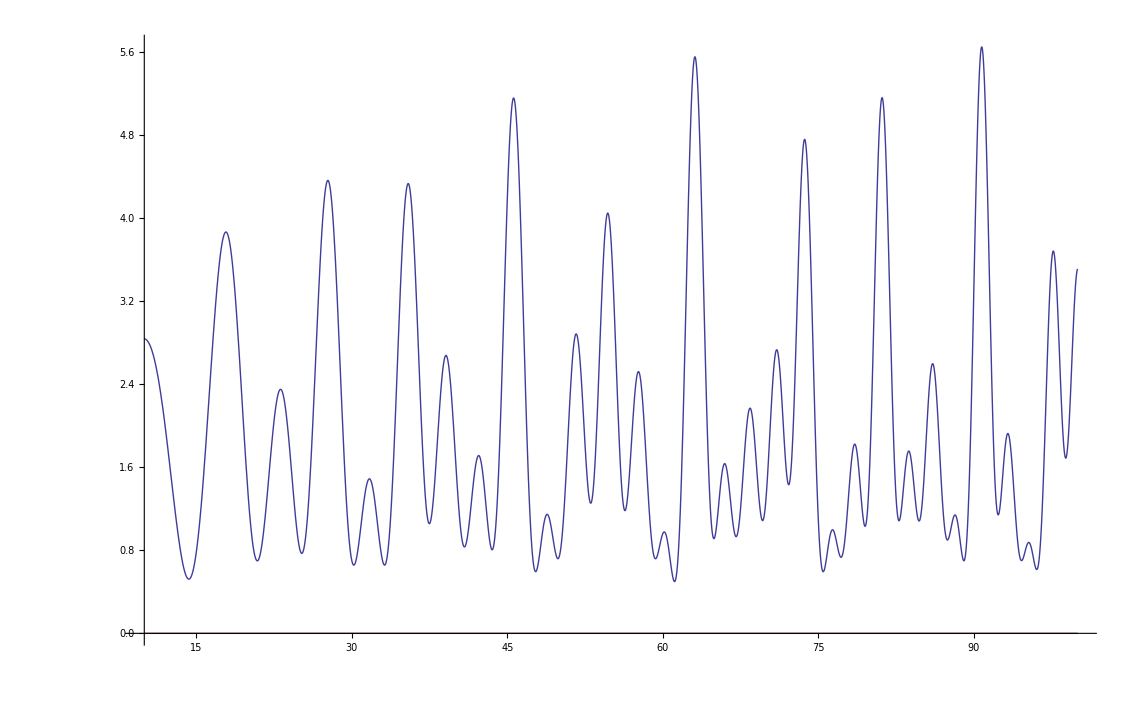

```mathematica
Plot[{Im@zb1[s+.4I]+Re@zb2[s+.4I], 0},{s,10,100}]
```

```mathematica
(* ???  This doesn't seem to cross the line 0 ever. *)
```

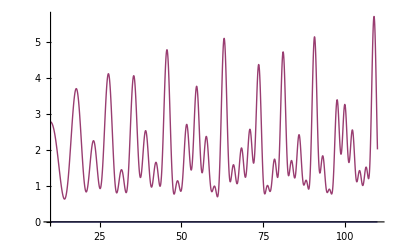

```mathematica
Plot[{0, Im@zb1[s+.5I]+Re@zb2[s+.5I]},{s,10,110}]
```

```mathematica
Integrate[Sin[s x]/x,{x,0,n}]
```

SinIntegral[n s]

```mathematica
Integrate[Cos[s x]/x,{x,2,n}]
```

ConditionalExpression[-CosIntegral[2 s]+CosIntegral[n s],Re[n]≥0||n∉Reals]

```mathematica
Sum[Sin[s x]/x,{x,1,n}]
```

1/2 ⅈ ⅇ^(-ⅈ s) (-(ⅇ^(-ⅈ s))^n LerchPhi[ⅇ^(-ⅈ s),1,1+n]+ⅇ^(2 ⅈ s) (ⅇ^(ⅈ s))^n LerchPhi[ⅇ^(ⅈ s),1,1+n]+ⅇ^(ⅈ s) Log[1-ⅇ^(ⅈ s)]-ⅇ^(ⅈ s) Log[ⅇ^(-ⅈ s) (-1+ⅇ^(ⅈ s))])

```mathematica
Sum[Cos[s x]/x,{x,1,n}]
```

-1/2 ⅇ^(-ⅈ s) ((ⅇ^(-ⅈ s))^n LerchPhi[ⅇ^(-ⅈ s),1,1+n]+ⅇ^(2 ⅈ s) (ⅇ^(ⅈ s))^n LerchPhi[ⅇ^(ⅈ s),1,1+n]+ⅇ^(ⅈ s) Log[1-ⅇ^(ⅈ s)]+ⅇ^(ⅈ s) Log[ⅇ^(-ⅈ s) (-1+ⅇ^(ⅈ s))])

```mathematica
pa[n_,s_]:=Sum[Sin[s x]/x,{x,1,n}]-Integrate[Sin[s x]/x,{x,0,n}]
pa2[n_,s_]:=Sum[Sin[s x]/x,{x,1,n}]-SinIntegral[n s]
ca[n_,s_]:=Integrate[(Cos[s Ceiling[x]]-Cos[s x])/x,{x,2,n}]
```

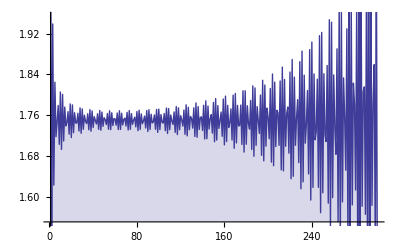

```mathematica
DiscretePlot[Re@pa2[n,-3.5-.02I],{n,1,300}]
```

```mathematica
Pi/4.
```

0.785398

```mathematica
Limit[(1/2 ⅈ ⅇ^(-ⅈ s) (-(ⅇ^(-ⅈ s))^n LerchPhi[ⅇ^(-ⅈ s),1,1+n]+ⅇ^(2 ⅈ s) (ⅇ^(ⅈ s))^n LerchPhi[ⅇ^(ⅈ s),1,1+n]+ⅇ^(ⅈ s) Log[1-ⅇ^(ⅈ s)]-ⅇ^(ⅈ s) Log[ⅇ^(-ⅈ s) (-1+ⅇ^(ⅈ s))]))-SinIntegral[n s],n->Infinity]
```

Limit[1/2 ⅈ ⅇ^(-ⅈ s) (-(ⅇ^(-ⅈ s))^n LerchPhi[ⅇ^(-ⅈ s),1,1+n]+ⅇ^(2 ⅈ s) (ⅇ^(ⅈ s))^n LerchPhi[ⅇ^(ⅈ s),1,1+n]+ⅇ^(ⅈ s) Log[1-ⅇ^(ⅈ s)]-ⅇ^(ⅈ s) Log[ⅇ^(-ⅈ s) (-1+ⅇ^(ⅈ s))])-SinIntegral[n s],n→∞]

```mathematica
Integrate[(Sin[s x]-Sin[Ceiling[s]x])/x,{x,0,n}]
```

SinIntegral[n s]-SinIntegral[n Ceiling[s]]

```mathematica
Limit[SinIntegral[n s]-SinIntegral[n Ceiling[s]],n->Infinity]
```

Limit[SinIntegral[n s]-SinIntegral[n Ceiling[s]],n→∞]

```mathematica
ca[100.,s]
```

$Aborted

```mathematica
Cos[s Log[j] + ArcTan[2s]]/.s->22+.1I/.j->7
```

0.947901-0.0719083 ⅈ

```mathematica
Cos[s Log[j] + Log[E^ArcTan[2s]]]/.s->22+.1I/.j->7
```

0.947901-0.0719083 ⅈ

```mathematica
Cos[s Log[j] + s Log[(E^ArcTan[2s])^(1/s)]]/.s->22+.1I/.j->7
```

0.947901-0.0719083 ⅈ

```mathematica
Cos[Log[j^s] + Log[(E^ArcTan[2s])]]/.s->22+.1I/.j->7
```

0.947901-0.0719083 ⅈ

```mathematica
Cos[Log[j^s E^ArcTan[2s]]]/.s->22+.1I/.j->7
```

0.947901-0.0719083 ⅈ

```mathematica
Cos[Log[j^s E^ArcTan[2s]]]
```

Cos[Log[ⅇ^ArcTan[2 s] j^s]]

```mathematica
FullSimplify@TrigToExp[ⅇ^ArcTan[2 s]]
```

(1-2 ⅈ s)^(ⅈ/2) (1+2 ⅈ s)^(-ⅈ/2)

```mathematica
Cos[Log[j^s (((1/2- ⅈ s)/(1/2+I s))^(ⅈ/2) )]]/.s->22+.1I/.j->7
```

0.947901-0.0719083 ⅈ

```mathematica
Cos[s Log[((1/2-ⅈ s)/(1/2+ⅈ s))^(ⅈ/(2 s)) j]]/.s->22+.1I/.j->7
```

0.947901-0.0719083 ⅈ